## Fun with Discrete Markov Processes

### Defined by Hector

```mathematica
ExponentialKernel[λ_,distance_]:=λ*ⅇ^(-λ*distance)
(*Markov - Calculates fraction of time mosquitoes spend at each network node, given a Markov process
migrationProbabilities = transitions probability matrix, calculated using Euclidean distances and a Kernel *)

CalculateMarkovSteadyState[migrationProbabilities_]:=Module[{initialState,markov,markovPDF},
initialState=ConstantArray[0,migrationProbabilities//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,migrationProbabilities];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
markovPDF
]
```

### Basic stuff

```mathematica
(* 
Call DiscreteMarkovProcess with two arguments:
First argument is the initial state;
  Second argument is the transitions matrix;
*)
markovTransitionMatrix = {{0,1/2,1/2},{1/2,0,1/2},{1/2,1/2,0}};
P = DiscreteMarkovProcess[{1,0,0},markovTransitionMatrix];
```

TemporalData[…]

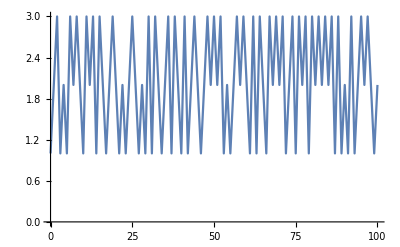

TemporalData[…]

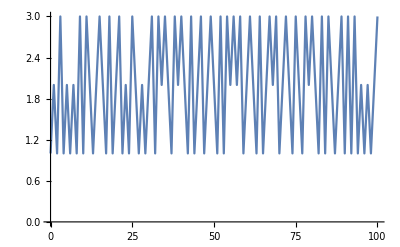

```mathematica
(* Here's how to generate a single trajectory, starting at the defined initial state *)
RandomFunction[P,{0,100}]
ListLinePlot[%]
(* And generate another one *)
RandomFunction[P,{0,100}]
ListLinePlot[%]
```

### Adding mosquito death

```mathematica
(* 
Add a node that represents mosquito death.
Each other node will have a transition probability to death.  For now we will have a constant hazard rate from each one.
To convert our given Transition Matrix we need to add a new element to each row and renormalize accordingly.
*)
markovTransitionMatrix = {{0,1/2,1/2},{1/2,0,1/2},{1/2,1/2,0}};
mosDeathMatrix = Join[Table[Join[markovTransitionMatrix[[i]]*.9,{.1},1],{i,1,Length[markovTransitionMatrix]}],{Join[Table[0,{i,1,Length[markovTransitionMatrix]}],{1.}]},1];

MatrixForm[mosDeathMatrix]
```

(0. | 0.45 | 0.45 | 0.1
0.45 | 0. | 0.45 | 0.1
0.45 | 0.45 | 0. | 0.1
0 | 0 | 0 | 1.)

TemporalData[…]

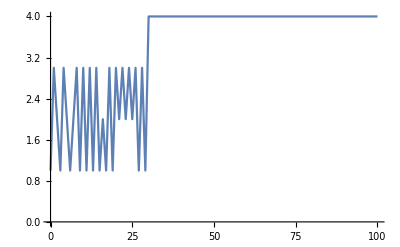

```mathematica
P = DiscreteMarkovProcess[{1,0,0,0},mosDeathMatrix];
SeedRandom[4]
RandomFunction[P,{0,100}]
ListLinePlot[%]
```

### Looking at distributions over time

```mathematica
(* Starting at node 1,
Probability weights after 1 time step *)
init = {1.,0,0,0};
init.mosDeathMatrix
```

{0.,0.45,0.45,0.1}

```mathematica
(* Starting at node 1,
Probability weights after 2 time steps *)
init = {1.,0,0,0};
init.MatrixPower[mosDeathMatrix,2]
```

{0.405,0.2025,0.2025,0.19}

```mathematica
(* Starting at node 1,
Probability weights after 3 time steps *)
init = {1.,0,0,0};
init.MatrixPower[mosDeathMatrix,3]
```

{0.18225,0.273375,0.273375,0.271}

```mathematica
(* Starting at node 1,
Probability weights after 4 time steps *)
init = {1.,0,0,0};
init.MatrixPower[mosDeathMatrix,4]
```

```mathematica
{0.24603750000000008,0.20503125000000005,0.20503125000000005,0.3439}
```

{0.246038,0.205031,0.205031,0.3439}

```mathematica
(* Starting at node 1,
Probability weights after 5 time steps *)
init = {1.,0,0,0};
init.MatrixPower[mosDeathMatrix,5]
```

{0.184528,0.202981,0.202981,0.40951}

```mathematica
h = init.MatrixPower[mosDeathMatrix,5];
h[[1;;-2]]/(1-h[[-1]])
```

{0.3125,0.34375,0.34375}

### Summing time spent at each spot over the lifetime of the mosquito

```mathematica
(* 
The idea here is that "time spent" at a spot is going to be proxy for biting. 
We also have to assume that mosquitoes start out infected, sort of.
*)

(* This will get MUCH trickier once we have different times spent at different locations *)
mosDeathMatrix
```

{{0.,0.45,0.45,0.1},{0.45,0.,0.45,0.1},{0.45,0.45,0.,0.1},{0,0,0,1.}}

```mathematica
init.MatrixPower[mosDeathMatrix,1]
init.MatrixPower[mosDeathMatrix,2]
init.MatrixPower[mosDeathMatrix,3]
init.MatrixPower[mosDeathMatrix,4]
```

{0.,0.45,0.45,0.1}

{0.405,0.2025,0.2025,0.19}

{0.18225,0.273375,0.273375,0.271}

{0.246038,0.205031,0.205031,0.3439}

```mathematica
MatrixForm[Sum[MatrixPower[mosDeathMatrix,i],{i,1,100}]]
init.Sum[MatrixPower[mosDeathMatrix,i],{i,1,100}]
```

(2.79302 | 3.10337 | 3.10337 | 91.0002
3.10337 | 2.79302 | 3.10337 | 91.0002
3.10337 | 3.10337 | 2.79302 | 91.0002
0. | 0. | 0. | 100.)

{2.79302,3.10337,3.10337,91.0002}

```mathematica
(* No idea why this works: *)
mp = mosDeathMatrix;
mp[[-1,-1]]=0;
```

```mathematica
MatrixForm[Inverse[IdentityMatrix[4] - mp].mp]
MatrixForm[init.Inverse[IdentityMatrix[4] - mp].mp]
```

(2.7931 | 3.10345 | 3.10345 | 1.
3.10345 | 2.7931 | 3.10345 | 1.
3.10345 | 3.10345 | 2.7931 | 1.
0. | 0. | 0. | 0.)

(2.7931
3.10345
3.10345
1.)

### Verify by simulating

I want to sum across an ensemble of trajectories, finding the total amount of time spent at each place

```mathematica
MatrixForm[mosDeathMatrix]
MatrixForm[init]
```

(0. | 0.45 | 0.45 | 0.1
0.45 | 0. | 0.45 | 0.1
0.45 | 0.45 | 0. | 0.1
0 | 0 | 0 | 1.)

(1.
0
0
0)

```mathematica
P = DiscreteMarkovProcess[init,mosDeathMatrix];
```

```mathematica
mosEnsemble = RandomFunction[P, {1,100},100000];
```

```mathematica
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,5,1}][[-1]],{i,1,100}];
```

```mathematica
Total[pHistogram,1]/100000.
```

{2.78965,3.10526,3.09637,91.0087}

```mathematica
(* This comes pretty close - it does seem that summing over the number of times the ensemble of trajectories hits each spot corresponds to the quantities calculated above! *)
```

### Adding interventions:

Suppose I now want to add in some interventions, that kill mosquitoes faster when they hit certain spots.
In our example, I can make it so that if a mosquito reaches spot 2 then it has a 90% chance of dying instead of a 10% chance of dying.
Need to generalize out the way that we convert the transitions matrix into the mosquito death matrix.

```mathematica
markovTransitionMatrix = {{0,1/2,1/2},{1/2,0,1/2},{1/2,1/2,0}};
mosHazardRates = {0.1, 0.9,0.1};
mosDeathMatrix = Join[Table[Join[markovTransitionMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[markovTransitionMatrix]}],{Join[Table[0,{i,1,Length[markovTransitionMatrix]}],{1.}]},1];
```

```mathematica
(* Unsure of these results - how about simulating? *)
```

```mathematica
P = DiscreteMarkovProcess[init,mosDeathMatrix];
```

```mathematica
mosEnsemble = RandomFunction[P, {1,100},100000];
```

```mathematica
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,5,1}][[-1]],{i,1,100}];
```

```mathematica
Total[pHistogram,1]/100000.
```

{0.33736,0.89354,0.6492,98.1199}

```mathematica
mosEnsemble = RandomFunction[P, {0,10},1000];
```

```mathematica
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,5,1}][[-1]],{i,1,10}];
```

```mathematica
Total[pHistogram,1]/1000.
```

{0.348,0.884,0.669,8.099}

Trying again with a larger matrix, to see just how asymmetric things get

```mathematica
markovTransitionMatrix  = 1/9.*(1 - IdentityMatrix[10]);
mosHazardRates = Table[0.1,{i,1,10}];
mosHazardRates[[4]] = 0.9;
mosHazardRates[[7]] = 0.9;
init = Table[0,{i,1,11}];
init[[1]] = 1;
```

```mathematica
mosDeathMatrix = Join[Table[Join[markovTransitionMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[markovTransitionMatrix]}],{Join[Table[0,{i,1,Length[markovTransitionMatrix]}],{1.}]},1];
MatrixForm[mosDeathMatrix]
```

(0. | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0. | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0. | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.0111111 | 0.0111111 | 0.0111111 | 0. | 0.0111111 | 0.0111111 | 0.0111111 | 0.0111111 | 0.0111111 | 0.0111111 | 0.9
0.1 | 0.1 | 0.1 | 0.1 | 0. | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0. | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.0111111 | 0.0111111 | 0.0111111 | 0.0111111 | 0.0111111 | 0.0111111 | 0. | 0.0111111 | 0.0111111 | 0.0111111 | 0.9
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0. | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0. | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0. | 0.1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
Length[{.1,.1,.1,.1,.1,.1,.1,.1,.1,0}]
{.1,.1,.1,.1,.1,.1,.1,.1,.1,.1,0}.Inverse[IdentityMatrix[11] - mp].mp
```

10

{0.26255,0.26255,0.26255,0.294422,0.26255,0.26255,0.294422,0.26255,0.26255,0.26255,1.}

```mathematica
(* And the time spent over each mosquito's lifetime *)
(* No idea why this works: *)
mp = mosDeathMatrix;
mp[[-1,-1]]=0;
MatrixForm[Inverse[IdentityMatrix[11] - mp].mp]
MatrixForm[init.Inverse[IdentityMatrix[11] - mp].mp]
MatrixForm[{.1,.1,.1,.1,.1,.1,.1,.1,.1,.1,0}.Inverse[IdentityMatrix[11] - mp].mp]
```

(0.238682 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.329591 | 1.
0.329591 | 0.238682 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.329591 | 1.
0.329591 | 0.329591 | 0.238682 | 0.358566 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.329591 | 1.
0.0398406 | 0.0398406 | 0.0398406 | 0.0323541 | 0.0398406 | 0.0398406 | 0.0433431 | 0.0398406 | 0.0398406 | 0.0398406 | 1.
0.329591 | 0.329591 | 0.329591 | 0.358566 | 0.238682 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.329591 | 1.
0.329591 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.238682 | 0.358566 | 0.329591 | 0.329591 | 0.329591 | 1.
0.0398406 | 0.0398406 | 0.0398406 | 0.0433431 | 0.0398406 | 0.0398406 | 0.0323541 | 0.0398406 | 0.0398406 | 0.0398406 | 1.
0.329591 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.358566 | 0.238682 | 0.329591 | 0.329591 | 1.
0.329591 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.238682 | 0.329591 | 1.
0.329591 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.358566 | 0.329591 | 0.329591 | 0.238682 | 1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

(0.238682
0.329591
0.329591
0.358566
0.329591
0.329591
0.358566
0.329591
0.329591
0.329591
1.)

(0.26255
0.26255
0.26255
0.294422
0.26255
0.26255
0.294422
0.26255
0.26255
0.26255
1.)

```mathematica
(* Verifying the weirdness with simulations *)
P = DiscreteMarkovProcess[init,mosDeathMatrix];
mosEnsemble = RandomFunction[P, {0,10},10000];
pHistogram = Table[HistogramList[mosEnsemble["SliceData",i],{1,12,1}][[-1]],{i,1,10}];
```

```mathematica
Total[pHistogram,1]/1000.
```

{2.237,3.217,3.187,3.519,3.196,3.136,3.429,3.068,3.159,3.21,68.642}